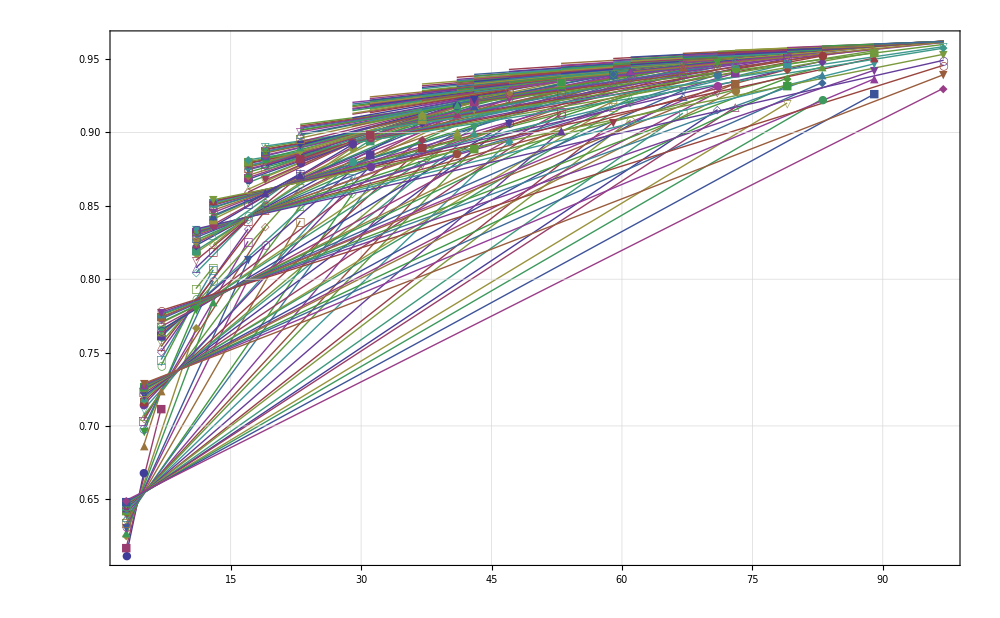

```mathematica
CloseStreams[];ListPlot[
Table[
Table[{p,RatioFor[tuple,{p}]}, {p, tuple}]
,{tuple, Subsets[Prime[Range[2,25]],{2}]}
]
, PlotMarkers->{Automatic,Tiny},
PlotRange->All,
GridLines->{Automatic,Append[Table[t,{t,0,1,0.1}],{0.45,{Red,Thick}}]},
Joined->True,
Frame->True,
ImageSize->1000
]
```

```mathematica
Length[Subsets[Prime[Range[2,10]],{3}]]
```

84

```mathematica
Subsets[Prime[Range[2,25]],{2}]
```

{{3,5},{3,7},{3,11},{3,13},{3,17},{3,19},{3,23},{3,29},{3,31},{3,37},{3,41},{3,43},{3,47},{3,53},{3,59},{3,61},{3,67},{3,71},{3,73},{3,79},{3,83},{3,89},{3,97},{5,7},{5,11},{5,13},{5,17},{5,19},{5,23},{5,29},{5,31},{5,37},{5,41},{5,43},{5,47},{5,53},{5,59},{5,61},{5,67},{5,71},{5,73},{5,79},{5,83},{5,89},{5,97},{7,11},{7,13},{7,17},{7,19},{7,23},{7,29},{7,31},{7,37},{7,41},{7,43},{7,47},{7,53},{7,59},{7,61},{7,67},{7,71},{7,73},{7,79},{7,83},{7,89},{7,97},{11,13},{11,17},{11,19},{11,23},{11,29},{11,31},{11,37},{11,41},{11,43},{11,47},{11,53},{11,59},{11,61},{11,67},{11,71},{11,73},{11,79},{11,83},{11,89},{11,97},{13,17},{13,19},{13,23},{13,29},{13,31},{13,37},{13,41},{13,43},{13,47},{13,53},{13,59},{13,61},{13,67},{13,71},{13,73},{13,79},{13,83},{13,89},{13,97},{17,19},{17,23},{17,29},{17,31},{17,37},{17,41},{17,43},{17,47},{17,53},{17,59},{17,61},{17,67},{17,71},{17,73},{17,79},{17,83},{17,89},{17,97},{19,23},{19,29},{19,31},{19,37},{19,41},{19,43},{19,47},{19,53},{19,59},{19,61},{19,67},{19,71},{19,73},{19,79},{19,83},{19,89},{19,97},{23,29},{23,31},{23,37},{23,41},{23,43},{23,47},{23,53},{23,59},{23,61},{23,67},{23,71},{23,73},{23,79},{23,83},{23,89},{23,97},{29,31},{29,37},{29,41},{29,43},{29,47},{29,53},{29,59},{29,61},{29,67},{29,71},{29,73},{29,79},{29,83},{29,89},{29,97},{31,37},{31,41},{31,43},{31,47},{31,53},{31,59},{31,61},{31,67},{31,71},{31,73},{31,79},{31,83},{31,89},{31,97},{37,41},{37,43},{37,47},{37,53},{37,59},{37,61},{37,67},{37,71},{37,73},{37,79},{37,83},{37,89},{37,97},{41,43},{41,47},{41,53},{41,59},{41,61},{41,67},{41,71},{41,73},{41,79},{41,83},{41,89},{41,97},{43,47},{43,53},{43,59},{43,61},{43,67},{43,71},{43,73},{43,79},{43,83},{43,89},{43,97},{47,53},{47,59},{47,61},{47,67},{47,71},{47,73},{47,79},{47,83},{47,89},{47,97},{53,59},{53,61},{53,67},{53,71},{53,73},{53,79},{53,83},{53,89},{53,97},{59,61},{59,67},{59,71},{59,73},{59,79},{59,83},{59,89},{59,97},{61,67},{61,71},{61,73},{61,79},{61,83},{61,89},{61,97},{67,71},{67,73},{67,79},{67,83},{67,89},{67,97},{71,73},{71,79},{71,83},{71,89},{71,97},{73,79},{73,83},{73,89},{73,97},{79,83},{79,89},{79,97},{83,89},{83,97},{89,97}}